```mathematica
R=0.25;
x0 = 0.5;
y0=0.5;
Co=8;
B=Co/Pi;
F=2*Sqrt[1000000];
```

```mathematica
NPoints=20;
Dim=2;
Points=RandomReal[1,{NPoints,Dim},WorkingPrecision->20]
```

```mathematica
N[B]
N[F]
```

```mathematica
NormSquare[x_,y_]:=(x-x0)*(x-x0) + (y-y0)*(y-y0)
Arc[x_,y_]:=F*(R*R- NormSquare[x,y]);
U[x_,y_]:=B x (x-1) y (y-1) (Pi + 2 ArcTan[Arc[x,y]])
DerivUdx[x_,y_]:=Derivative[1,0][U][x,y]
DerivUdy[x_,y_]:=Derivative[0,1][U][x,y]
Gradiente[x_,y_]:=Sqrt[DerivUdx[x,y]*DerivUdx[x,y]+DerivUdy[x,y]*DerivUdy[x,y]]
DerivU2dxdx[x_,y_]:=Derivative[2,0][U][x,y]
DerivU2dydy[x_,y_]:=Derivative[0,2][U][x,y]
DerivU2dxdy[x_,y_]:=Derivative[1,1][U][x,y]
```

```mathematica
For[i=1,i<NPoints+1,i++,AA=Points[[i,1]];BB=Points[[i,2]];Print[i];MM={U[AA,BB],DerivUdx[AA,BB],DerivUdy[AA,BB],DerivU2dxdx[AA,BB],DerivU2dxdy[AA,BB],DerivU2dydy[AA,BB]};Print[SetPrecision[{AA,BB,MM},20]]]
```

```mathematica
X0=0.6319054056258069;
Y0=0.03079417253097617;
NormSquare[X0,Y0]
Arc[X0,Y0]
U[X0,Y0]
DerivUdx[X0,Y0]
DerivUdy[X0,Y0]
Gradiente[X0,Y0]
DerivU2dxdx[X0,Y0]
DerivU2dydy[X0,Y0]
DerivU2dxdy[X0,Y0]
```

```mathematica
X0=0.;
Y0=0.14792933031195624;
NormSquare[X0,Y0]
Arc[X0,Y0]
U[X0,Y0]
DerivUdx[X0,Y0]
Gradiente[X0,Y0]
DerivU2dxdx[X0,Y0]
DerivU2dydy[X0,Y0]
```

```mathematica
X0=0.75635417258082427;
Y0=0.53698233257798900;
NormSquare[X0,Y0]
Arc[X0,Y0]
U[X0,Y0]
Gradiente[X0,Y0]
DerivU2dxdx[X0,Y0]
DerivU2dydy[X0,Y0]
DerivU2dxdx[X0,Y0]+DerivU2dydy[X0,Y0]
```

```mathematica
X0=0.5;
Y0=0.5;
NormSquare[X0,Y0]
Arc[X0,Y0]
U[X0,Y0]
Gradiente[X0,Y0]
DerivU2dxdx[X0,Y0]
DerivU2dydy[X0,Y0]
```

## Nova Função Arc Tan para testar

```mathematica
ArcTan[0]
```

0

```mathematica
R=0.25;
x0=0.5;
y0=0.5;
z0 = 0.5;
KVal=1000000;
F=Sqrt[KVal];
w[x_,y_]:=F (R^2 -((x-x0)^2 + (y-y0)^2 ))
u[x_,y_]:=5* x (1-x) y (1-y) (.5*Pi+ArcTan[w[x,y]])
```

```mathematica
w1[x_]:=F*(R*R-((x-x0)^2))
u1[x_]:=(5/4.) x (1-x) (.5*Pi+ArcTan[w1[x]])
```

```mathematica
w3[x_,y_,z_]:=F (R^2 -((x-x0)^2 + (y-y0)^2 +(z-z0)^2))
u3[x_,y_,z_]:=20* x (1-x) y (1-y) z (1-z) (.5*Pi+ArcTan[w3[x,y,z]])
```

```mathematica
Plot[u1[x],{x,0,1}]
```

```mathematica
Plot3D[u[x,y],{x,0,1.},{y,0,1.}]
```

```mathematica
u3[.5,0.5,0.5]
```

0.976748

```mathematica
Plot3D[u3[x,y,0.75],{x,0,1},{y,0,1},PlotRange->All]
```

```mathematica
Dudx[x_,y_]:=Derivative[1,0][u][x,y]
D2udx2[x_,y_]:=Derivative[2,0][u][x,y]
D2udy2[x_,y_]:=Derivative[0,2][u][x,y]
D2udydx[x_,y_]:=Derivative[1,1][u][x,y]
Laplacia[x_,y_]:=D2udx2[x,y]+D2udy2[x,y]
```

```mathematica
DudxEu[x_,y_]:=5 y (1-y) ((1-2 x)(.5*Pi + ArcTan[w[x,y]])-((2*F*(x-x0) x (1-x))/(1+w[x,y]*w[x,y])))
D2udx2Eu[x_,y_]:=-5 y (1-y) (2 (.5*Pi+ArcTan[w[x,y]])-2*F*((5 x x-4 x x0 -3 x+2 x0)/(1+w[x,y]*w[x,y]))+8*F*F*((x (1-x) w[x,y] (x-x0) (x-x0))/((1+w[x,y]*w[x,y])  (1+w[x,y]*w[x,y]))))
D2udydxEu[x_,y_]:=5 ((1-2 y) (1-2 x) (.5*Pi+ArcTan[w[x,y]]) - 2*F (((x-x0) x (1-x) (1-2 y) + (y-y0) (1-y) y (1-2 x))/(1+w[x,y]*w[x,y]))-8 F F x (1-x) y (1-y) (x-x0) (y-y0) (w[x,y]/((1+w[x,y]*w[x,y])  (1+w[x,y]*w[x,y]))))
Poli[a_,b_]:=5 a a -4 a b-3 a+2 b
LaplacianEu[x_,y_]:=(-10) ((y (1-y) + x (1-x)) (.5*Pi+ArcTan[w[x,y]]) - (F/(1+w[x,y]*w[x,y])) (y (1-y) Poli[x,x0] + x (1-x) Poli[y,y0])+(4 F F x (1-x) y (1-y) w[x,y] ((x-x0) (x-x0) + (y-y0) (y-y0)) (1./((1+w[x,y]*w[x,y]) (1+w[x,y]*w[x,y])))))
```

```mathematica
Diff[x_,y_]:=Dudx[x,y]-DudxEu[x,y]
Diff2[x_,y_]:=D2udx2[x,y]-D2udx2Eu[x,y]
Diffxy[x_,y_]:=D2udydx[x,y]-D2udydxEu[x,y]
DiffLap[x_,y_]:=Laplacia[x,y]-LaplacianEu[x,y]
```

```mathematica
X=0.00293188;
Y=0.014422834;
Diff[X,Y]
Diff2[X,Y]
Diffxy[X,Y]
DiffLap[X,Y]
```

-2.71051×10^-20

-5.42101×10^-20

0.

1.0842×10^-19

## Testes no 13/11/2013

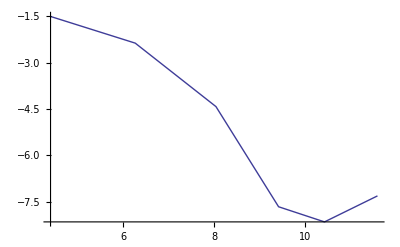

```mathematica
NEquations={81,525,3117,12413,34189,109997};
L2Error={0.222637,0.0938794,0.0120296,0.000470121,0.000287966,0.00066824};
LogNEquations=Table[Log[NEquations[[i]]],{i,1,Length[NEquations]}];
LogL2Errors=Table[Log[L2Error[[i]]],{i,1,Length[L2Error]}];
ListPlot[Table[{LogNEquations[[i]],LogL2Errors[[i]]},{i,1,Length[LogNEquations]}],Joined->True]
```

```mathematica
NEquations={81,525,3217,10725,28069,84453};
L2Error={0.222637,0.0938794,0.0120282,0.000470343,0.000276476,0.000386916};
LogNEquations=Table[Log[NEquations[[i]]],{i,1,Length[NEquations]}];
LogL2Errors=Table[Log[L2Error[[i]]],{i,1,Length[L2Error]}];
ListPlot[Table[{LogNEquations[[i]],LogL2Errors[[i]]},{i,1,Length[LogNEquations]}],Joined->True]
```

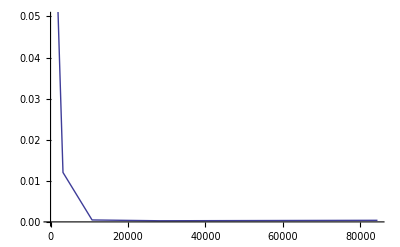

```mathematica
ListPlot[Table[{NEquations[[i]],L2Error[[i]]},{i,1,Length[NEquations]}],Joined->True,PlotRange->{0.0,0.05}]
```

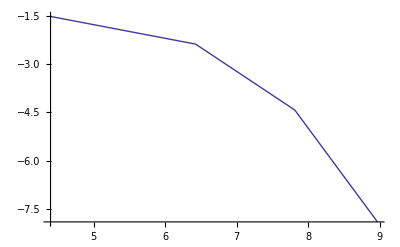

```mathematica
NEquations={81,617,2473,7869,26685};
L2Error={0.222637,0.0939309,0.0120006,0.000364794,7.04117e-005};
LogNEquations=Table[Log[NEquations[[i]]],{i,1,Length[NEquations]}];
LogL2Errors=Table[Log[L2Error[[i]]],{i,1,Length[L2Error]}];
ListPlot[Table[{LogNEquations[[i]],LogL2Errors[[i]]},{i,1,Length[LogNEquations]}],Joined->True]
```

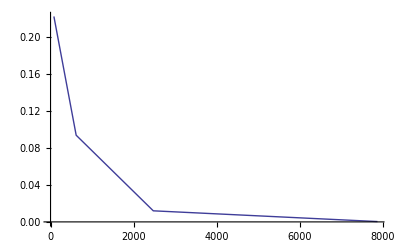

```mathematica
NEquations={81,617,2473,7869,26685};
L2Error={0.222637,0.0939309,0.0120006,0.000364794,7.04117e-005};
LogNEquations=Table[Log[NEquations[[i]]],{i,1,Length[NEquations]}];
LogL2Errors=Table[Log[L2Error[[i]]],{i,1,Length[L2Error]}];
ListPlot[Table[{NEquations[[i]],L2Error[[i]]},{i,1,Length[LogNEquations]}],Joined->True]
```